```mathematica
<<MaTeX`
ClearAll[plotColors];
plotColors::usage="plotColors[plotType,plotTheme] gives a list of the colors used in a plot when several curves are drawn. Here plotType is, for example, Plot or ListLogPlot while plotTheme may be \"Scientific\", \"Classic\" etc.";
plotColors[plotType_,plotTheme_]:=("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme[plotTheme,plotType]))/.Directive[x_,__]:>x;
pltcolors=plotColors[ListLinePlot,"Scientific"];
```

### MaTeX

```mathematica
magnificationaxes=1.;
magnificationlegends=1.;
latex411=MaTeX["D^+",Magnification->magnificationlegends,ContentPadding->False];
latex431=MaTeX["D_s^+",Magnification->magnificationlegends,ContentPadding->False];
latex411bar=MaTeX["D^-",Magnification->magnificationlegends,ContentPadding->False];
latex431bar=MaTeX["D_s^-",Magnification->magnificationlegends,ContentPadding->False];
latexpythia=MaTeX["\\text{PYTHIA8}",Magnification->magnificationlegends,ContentPadding->False];
latexgaussian=MaTeX["\\text{Gaussian}",Magnification->magnificationlegends,ContentPadding->False];
latexold=MaTeX["(1+|x_F|)^n",Magnification->magnificationlegends,ContentPadding->False];
latexoldb=MaTeX["b=1.08",Magnification->magnificationlegends,ContentPadding->False];
latexnewb=MaTeX["b=0.63",Magnification->magnificationlegends,ContentPadding->False];
xlabel=MaTeX["E \\text{(GeV)}",Magnification->magnificationaxes,ContentPadding->False];
xlabelpt2=MaTeX["pT^2 (\\text{GeV}^2)",Magnification->magnificationaxes,ContentPadding->False];
ylabel=MaTeX["info*\\frac{d\\sigma}{dE}",Magnification->magnificationaxes,ContentPadding->False];
ylabelpt2=MaTeX["info*\\frac{d\\sigma}{dpT^2}",Magnification->magnificationaxes,ContentPadding->False];
```

### Data

```mathematica
xf=Import[NotebookDirectory[]<>"xf.dat"];
pt2=Import[NotebookDirectory[]<>"pt2.dat"];
```

```mathematica
xftable={}; (*411, 431, 411bar, 431bar*)
Do[
xdata=Table[xf[[i,1]]+(xf[[i,2]]-xf[[i,1]])/xf[[i,3]]*j,{j,0,xf[[i,3]]-1}];
ydata=Table[xf[[i,j]],{j,4,xf[[i,3]]+3}];
auxtable=Table[{xdata[[j]],ydata[[j]]},{j,1,Dimensions[xdata][[1]]}];
AppendTo[xftable,auxtable]
,{i,1,4}]
pt2table={}; (*411, 431, 411bar, 431bar*)
Do[
xdata=Table[pt2[[i,1]]+(pt2[[i,2]]-pt2[[i,1]])/pt2[[i,3]]*j,{j,0,pt2[[i,3]]-1}];
ydata=Table[pt2[[i,j]],{j,4,pt2[[i,3]]+3}];
auxtable=Table[{xdata[[j]],ydata[[j]]},{j,1,Dimensions[xdata][[1]]}];
AppendTo[pt2table,auxtable]
,{i,1,4}]
```

## Plots by flavour

### xF plots D431

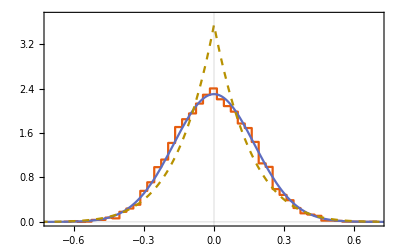

```mathematica
plotrange={{-0.7,0.7},{0,3.7}};
framelabel={xlabel,ylabel};
legends={latexpythia,latexgaussian,latexold};
plotlegends=Placed[LineLegend[{pltcolors[[1]],pltcolors[[2]],{Dashed,pltcolors[[8]]}},legends,Spacings->0.01,LegendLayout->{"Column",1},LegendMarkerSize->16
],{0.825,0.8}];
imagesize={{300},Automatic};
frametickstyle=Directive[Black];
imagepadding={{50,3},{40,1}};
a=16.6339541;
n=6.1;
text=Graphics[Text[latex431,Scaled[{0.1,0.9}]]];
listplot=ListStepPlot[{xftable[[2]]},PlotStyle->{pltcolors[[1]]}];
newplot=Plot[√(a/Pi)Exp[-a*x^2],{x,-1,1},PlotStyle->pltcolors[[2]]];
oldplot=Plot[(n+1)/2*(1-Abs[x])^n,{x,-1,1},PlotStyle->{Dashed,pltcolors[[8]]}];
bg=Plot[{,,,},{x,-1,1},PlotTheme->"Scientific",PlotRange->plotrange,AspectRatio->1/GoldenRatio,PlotLegends->plotlegends,FrameLabel->framelabel,ImageSize->imagesize,ImagePadding->imagepadding,FrameTicksStyle->frametickstyle];
plotexp=Show[bg,listplot,newplot,oldplot]
Export[NotebookDirectory[]<>"plot-fit431xf.pdf",plotexp];
```

### pt2 plots D431

0.63424

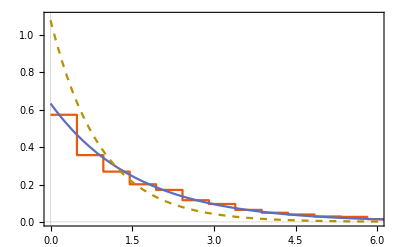

```mathematica
plotrange={{0,6},{0,1.1}};
framelabel={xlabelpt2,ylabelpt2};
legends={latexpythia,latexnewb,latexoldb};
plotlegends=Placed[LineLegend[{pltcolors[[1]],pltcolors[[2]],{Dashed,pltcolors[[8]]}},legends,Spacings->0.01,LegendLayout->{"Column",1},LegendMarkerSize->16
],{0.825,0.8}];
imagesize={{300},Automatic};
frametickstyle=Directive[Black];
imagepadding={{50,3},{40,1}};
a=16.6339541;
oldb=1.08;
newb=0.63424038
text=Graphics[Text[latex431,Scaled[{0.1,0.9}]]];
listplot=ListStepPlot[{pt2table[[2]]},PlotStyle->{pltcolors[[1]]},PlotRange->All];
oldplot=Plot[oldb*Exp[-oldb*x],{x,0,20},PlotStyle->{Dashed,pltcolors[[8]]},PlotPoints->200,PlotRange->All];
newplot=Plot[newb*Exp[-newb*x],{x,0,20},PlotStyle->pltcolors[[2]],PlotRange->All];
bg=Plot[{,,,},{x,0,1},PlotTheme->"Scientific",PlotRange->plotrange,AspectRatio->1/GoldenRatio,PlotLegends->plotlegends,FrameLabel->framelabel,ImageSize->imagesize,FrameTicksStyle->frametickstyle,ImagePadding->imagepadding];
plotexp=Show[bg,listplot,newplot,oldplot]
Export[NotebookDirectory[]<>"plot-fit431pt2.pdf",plotexp];
```

## Plots Dall

### xF plots-Dall

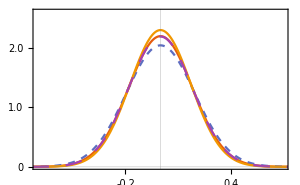

```mathematica
plotrange={{-0.7,0.7},{0.01,2.6}};
framelabel={xlabel,ylabel};
legends={latex411,latex411bar,latex431,latex431bar};
d411color=pltcolors[[1]];
d411barcolor=pltcolors[[2]];
d431color=pltcolors[[3]];
d431barcolor=pltcolors[[4]];
plotlegends=Placed[LineLegend[{d411color,{Dashed,d411barcolor},d431color,{Dashed,d431barcolor}},legends,Spacings->0.01,LegendLayout->{"Column",2},LegendMarkerSize->16
],{0.825,0.825}];
imagesize={300,Automatic};
frametickstyle=Directive[Black];
imagepadding={{60,3},{40,1}};
scalingfunctions={"Linear","Linear"};
a411=15.1914842;
a431=16.6339541;
a411bar=13.1260718;
a431bar=15.09998238;
newplot411=Plot[√(a411/Pi)Exp[-a411*x^2],{x,-1,1},PlotStyle->d411color,ScalingFunctions->scalingfunctions];
newplot411bar=Plot[√(a411bar/Pi)Exp[-a411bar*x^2],{x,-1,1},PlotStyle->{Dashed,d411barcolor},ScalingFunctions->scalingfunctions];
newplot431=Plot[√(a431/Pi)Exp[-a431*x^2],{x,-1,1},PlotStyle->d431color,ScalingFunctions->scalingfunctions];
newplot431bar=Plot[√(a431bar/Pi)Exp[-a431bar*x^2],{x,-1,1},PlotStyle->{Dashing[{0.04}],d431barcolor},ScalingFunctions->scalingfunctions];

bg=Plot[{,,,},{x,-1,1},ScalingFunctions->scalingfunctions,PlotTheme->"Scientific",PlotRange->plotrange,AspectRatio->1/GoldenRatio,PlotLegends->plotlegends,FrameLabel->framelabel,ImageSize->imagesize,ImagePadding->imagepadding,FrameTicksStyle->frametickstyle];
plotexp=Show[bg,newplot411,newplot411bar,newplot431,newplot431bar]
Export[NotebookDirectory[]<>"plot-fitxfDall.pdf",plotexp];
```

### pT2 plots-Dall

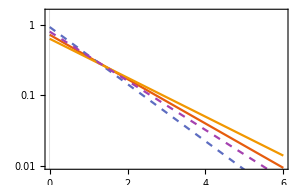

```mathematica
plotrange={{0,6},{0.01,1.5}};
framelabel={xlabelpt2,ylabelpt2};
legends={latex411,latex411bar,latex431,latex431bar};
d411color=pltcolors[[1]];
d411barcolor=pltcolors[[2]];
d431color=pltcolors[[3]];
d431barcolor=pltcolors[[4]];
plotlegends=Placed[LineLegend[{d411color,{Dashed,d411barcolor},d431color,{Dashed,d431barcolor}},legends,Spacings->0.01,LegendLayout->{"Column",2},LegendMarkerSize->16
],{0.825,0.825}];
imagesize={300,Automatic};
frametickstyle=Directive[Black];
imagepadding={{60,3},{40,1}};
scalingfunctions={"Linear","Log"};
b411=0.7224411;
b431=0.63424038;
b411bar=0.92910691;
b431bar=0.80034524;
newplot411=Plot[b411*Exp[-b411*x],{x,0,6},PlotRange->All,PlotStyle->d411color,ScalingFunctions->scalingfunctions];
newplot411bar=Plot[b411bar*Exp[-b411bar*x],{x,0,6},PlotRange->All,PlotStyle->{Dashed,d411barcolor},ScalingFunctions->scalingfunctions];
newplot431=Plot[b431*Exp[-b431*x],{x,0,6},PlotRange->All,PlotStyle->d431color,ScalingFunctions->scalingfunctions];
newplot431bar=Plot[b431bar*Exp[-b431bar*x],{x,0,6},PlotRange->All,PlotStyle->{Dashed,d431barcolor},ScalingFunctions->scalingfunctions];
bg=Plot[{,,,},{x,0,6},ScalingFunctions->scalingfunctions,PlotTheme->"Scientific",PlotRange->plotrange,AspectRatio->1/GoldenRatio,PlotLegends->plotlegends,FrameLabel->framelabel,ImageSize->imagesize,ImagePadding->imagepadding,FrameTicksStyle->frametickstyle];
plotexp=Show[bg,newplot411,newplot411bar,newplot431,newplot431bar]
Export[NotebookDirectory[]<>"plot-fitpT2Dall.pdf",plotexp];
```

```mathematica
300*1/N[GoldenRatio]
```

185.41